```mathematica
(* Wilson confidence interval (CI) for the Binomial distribution parameter. 
- jj: count of successes
- nn: count of attempts
- confLvl: confidence level for the CI *) 
interWilson[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]];
```

```mathematica
(*** STATIC EXAMPLE ANALYSIS ***)
```

```mathematica
(* probabilistic programming *) 
statDataPP = Import[NotebookDirectory[]<>"../testing/static/static_ex_proof_2.csv"][[2;;All, 2;;4]] (* removing the header and the counter *) ;
statDataOur= Import[NotebookDirectory[]<>"../testing/static/output_our_tool.csv"];
```

```mathematica
statDataPPSlices = Table[statDataPP[[1;;i]], {i, 1, Length@statDataPP}] ;
statDataOurSlices = Table[statDataOur[[1;;i]], {i, 1, Length@statDataOur}] ;
```

```mathematica
(* marginal prob of first variable being day *)
```

```mathematica
interWilson[Count[statDataPP[[All,1]], "day"],Length@statDataPP[[All,1]], 0.95]
interWilson[Count[statDataOur[[All,1]], "day"],Length@statDataOur[[All,1]], 0.95]
```

Interval[{0.557214,0.618113}]

Interval[{0.571327,0.631892}]

```mathematica
ints1 = interWilson[Count[#[[All,1]], "day"],Length@#, 0.95]&/@ statDataPPSlices;
ints2 = interWilson[Count[#[[All,1]], "day"],Length@#, 0.95]&/@ statDataOurSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

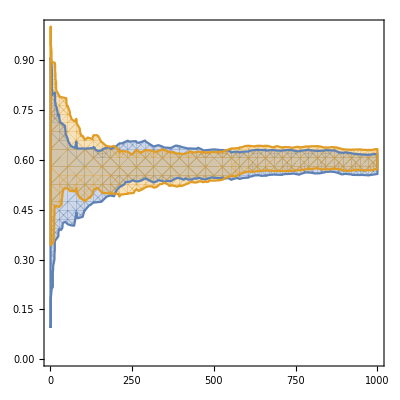

```mathematica
RegionPlot[{IntervalMemberQ[ints1[[ Ceiling@x ]], y], IntervalMemberQ[ints2[[ Ceiling@x ]], y]},{x,1,1000},{y,0,1}]
```

```mathematica
(* marginal prob of second variable being detected *)
```

```mathematica
interWilson[Count[statDataPP[[All,2]], "detected"],Length@statDataPP[[All,2]], 0.95]
interWilson[Count[statDataOur[[All,2]], "detected"],Length@statDataOur[[All,2]], 0.95]
```

Interval[{0.536091,0.597396}]

Interval[{0.550167,0.611213}]

```mathematica
ints3 = interWilson[Count[#[[All,2]], "detected"],Length@#, 0.95]&/@ statDataPPSlices;
ints4 = interWilson[Count[#[[All,2]], "detected"],Length@#, 0.95]&/@ statDataOurSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

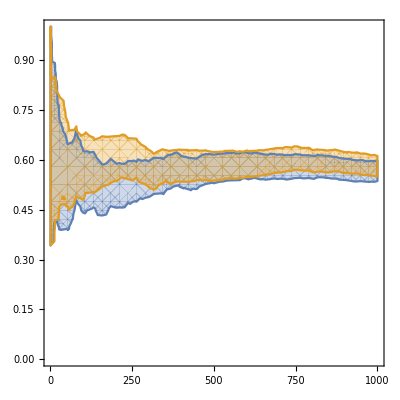

```mathematica
RegionPlot[{IntervalMemberQ[ints3[[ Ceiling@x ]], y], IntervalMemberQ[ints4[[ Ceiling@x ]], y]},{x,1,1000},{y,0,1}]
```

```mathematica
(* marginal prob of third variable being in *)
```

```mathematica
interWilson[Count[statDataPP[[All,3]], "in"],Length@statDataPP[[All,3]], 0.95]
interWilson[Count[statDataOur[[All,3]], "in"],Length@statDataOur[[All,3]], 0.95]
```

Interval[{0.76055,0.811253}]

Interval[{0.759511,0.8103}]

```mathematica
ints5 = interWilson[Count[#[[All,3]], "in"],Length@#, 0.95]&/@ statDataPPSlices;
ints6 = interWilson[Count[#[[All,3]], "in"],Length@#, 0.95]&/@ statDataOurSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

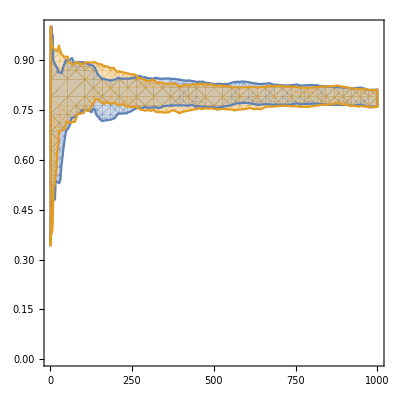

```mathematica
RegionPlot[{IntervalMemberQ[ints5[[ Ceiling@x ]], y], IntervalMemberQ[ints6[[ Ceiling@x ]], y]},{x,1,1000},{y,0,1}]
```

```mathematica
(* joint prob of all good *)
```

```mathematica
interWilson[Count[statDataPP, {"day", "detected", "in"}],Length@statDataPP, 0.95]
interWilson[Count[statDataOur, {"day", "detected", "in"}],Length@statDataOur, 0.95]
```

Interval[{0.33573,0.395303}]

Interval[{0.352391,0.412512}]

```mathematica
ints7 = interWilson[Count[#, {"day", "detected", "in"}],Length@#, 0.95]&/@ statDataPPSlices;
ints8 = interWilson[Count[#,{"day", "detected", "in"}],Length@#, 0.95]&/@ statDataOurSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

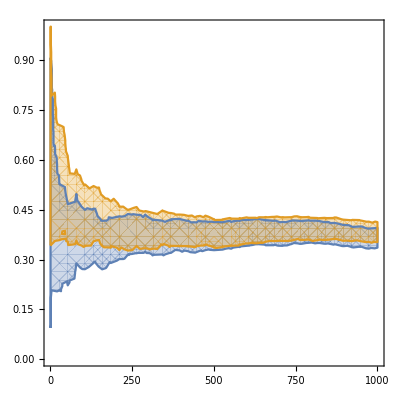

```mathematica
RegionPlot[{IntervalMemberQ[ints7[[ Ceiling@x ]], y], IntervalMemberQ[ints8[[ Ceiling@x ]], y]},{x,1,1000},{y,0,1}]
```

```mathematica
(* joint prob of all bad *)
```

```mathematica
interWilson[Count[statDataPP, {"night", "not detected", "out"}],Length@statDataPP, 0.95]
interWilson[Count[statDataOur, {"night", "not detected", "out"}],Length@statDataOur, 0.95]
```

Interval[{0.0312209,0.0562844}]

Interval[{0.0346625,0.0608122}]

```mathematica
ints9 = interWilson[Count[#,  {"night", "not detected", "out"}],Length@#, 0.95]&/@ statDataPPSlices;
ints10 = interWilson[Count[#, {"night", "not detected", "out"}],Length@#, 0.95]&/@ statDataOurSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

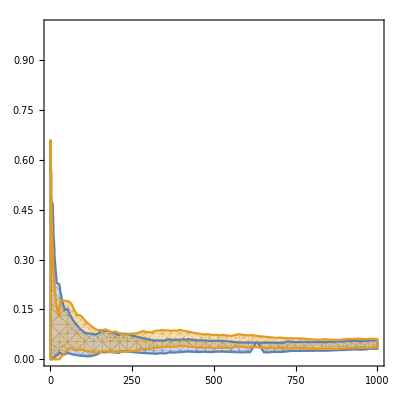

```mathematica
RegionPlot[{IntervalMemberQ[ints9[[ Ceiling@x ]], y], IntervalMemberQ[ints10[[ Ceiling@x ]], y]},{x,1,1000},{y,0,1}]
```

```mathematica
(*** INVARIANT EXAMPLE ANALYSIS ***)
```

```mathematica
invData = Import[NotebookDirectory[]<>"../testing/time_invariant/invariant_ex_testing.csv"][[2;;All, 2;;3]] (* removing the header and the counter *) ;
```

```mathematica
(* marginal prob of first variable being low *)
```

```mathematica
interWilson[Count[invData[[All,1]], "low"],Length@invData[[All,1]], 0.95]
```

Interval[{0.763669,0.814111}]

```mathematica
(* marginal prob of second variable being low*) 
interWilson[Count[invData[[All,2]], "low"],Length@invData[[All,2]], 0.95]
```

Interval[{0.437255,0.49899}]

```mathematica
(* joint prob of both low *)
```

```mathematica
interWilson[Count[invData, {"low", "low"}],Length@invData, 0.95]
```

Interval[{0.349448,0.409478}]

```mathematica
(* joint prob of both high *)
```

```mathematica
interWilson[Count[invData, {"high", "high"}],Length@invData, 0.95]
```

Interval[{0.102224,0.142677}]

```mathematica
(* calculate the difference between the estimated distributions ? *)
```